# HighPT

## Flavor bounds from high-p_T tails at LHC

Keep this notebook out of git !!!

## Preamble

#### Set package directory

Make sure that the package directory is in the $Path.

```mathematica
SetDirectory@ ParentDirectory@ NotebookDirectory[];
AppendTo[$Path, "/Users/dario/Dropbox/GitHub/HighPT"];
```

#### Loading the package

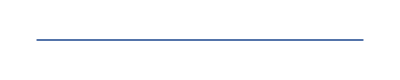

HighPT | : | High-p_T Tails
 |  | 
Authors | : | Lukas Allwicher, Darius A. Faroughy, Florentin Jaffredo,
 |  | Olcyr Sumensari, and Felix Wilsch
Reference | : | arXiv:22xx.xxxxxhttps://arxiv.org/Nonehttps://arxiv.org/HyperlinkHyperlinkActive
Website | : | https://github.com/HighPT/HighPThttps://github.com/HighPT/HighPTNonehttps://github.com/HighPT/HighPTHyperlinkHyperlinkActive

HighPT is free software under the terms of the MIT License.

Please submit bugs and feature requests using GitHub's issue system at:

https://github.com/HighPT/HighPT/issueshttps://github.com/HighPT/HighPT/issuesNonehttps://github.com/HighPT/HighPT/issuesHyperlinkHyperlinkActive

-Graphics-

Using model: SMEFT

Maximum operator mass dimension: 6

EFT series truncation at: Λ_NP^-4

```mathematica
<<HighPT`
```

#### FOR DEVELOPMENT ONLY

This allows to access all PackageScope functions in the notebook.
Remove this line eventually.

```mathematica
PrependTo[$ContextPath, "HighPT`PackageScope`"];
```

## SMEFT

```mathematica
LHCSearch[]//TableForm
```

<|di-tau-ATLAS→[arXiv:2002.12223](https://arxiv.org/abs/2002.12223),di-electron-CMS→[arXiv:2103.02708](https://arxiv.org/abs/2103.02708),mono-tau-ATLAS→[ATLAS-CONF-2021-025](https://cds.cern.ch/record/2773301/),mono-muon-ATLAS→[arXiv:1906.05609](https://arxiv.org/abs/1906.05609),mono-electron-ATLAS→[arXiv:1906.05609](https://arxiv.org/abs/1906.05609),muon-tau-CMS→[CMS-PAS-EXO-19-014](https://cds.cern.ch/record/2779023),electron-tau-CMS→[CMS-PAS-EXO-19-014](https://cds.cern.ch/record/2779023),electron-muon-CMS→[CMS-PAS-EXO-19-014](https://cds.cern.ch/record/2779023)|>

## Initialization of SMEFT

```mathematica
InitializeModel["SMEFT",
	EFTorder->4,
	OperatorDimension->6,
	Scale->2000
]
```

OptionValue::nodef: Unknown option Scale for InitializeModel.

Using model: SMEFT

Maximum operator mass dimension: 6

EFT series truncation at: Λ_NP^-4

```mathematica
mumuYield
```

{(-40.4773+7.41234×10^-20 ⅈ) Conjugate[WC[eq,{2,2,1,2}]]+1818+(0.238263-0.0135753 ⅈ) Conjugate[WC[uW,{2,2}]] WC[uW,{3,2}]+(0.00992075+6.55394×10^-21 ⅈ) Conjugate[WC[uW,{3,2}]] WC[uW,{3,2}],1,1,35,1,1,(-0.00289896-1.89341×10^-25 ⅈ) Conjugate[WC[eq,{2,2,1,2}]]+1823+(4.77582×10^-9+5.27877×10^-26 ⅈ) Conjugate[WC[uW,{3,2}]] WC[uW,{3,2}]}
 |  |  |  |

## Compute event yields for NC processes

Uncomment the needed yields below.

```mathematica
(*ττYield=EventYield["di-tau-ATLAS"]//EchoTiming;*)
```

```mathematica
(*μμYield=EventYield["di-muon-CMS"]//EchoTiming;*)
```

```mathematica
tataYield=EventYield[
	"di-tau-ATLAS",
	SM->False (* exclude the SM contribution *)
];
```

Computing observable for di-tau-ATLAS search: [arXiv:2002.12223](https://arxiv.org/abs/2002.12223)

PROCESS | : | pp → τ^-τ^+
EXPERIMENT | : | ATLAS
ARXIV | : | [2002.12223](https://arxiv.org/abs/2002.12223)
SOURCE | : | [hepdata](https://doi.org/10.17182/hepdata.93071.v4/t3)
OBSERVABLE | : | m_T^tot
BINNING m_T^tot [GeV] | : | {150,200,250,300,350,400,450,500,600,700,800,900,1000,1150,1500}
EVENTS OBSERVED | : | {1167., 1568., 1409., 1455., 1292., 650., 377., 288., 92., 57., 27., 14., 11., 13.}
LUMINOSITY [fb^-1] | : | 139
BINNING √(ŝ) [GeV] | : | {150,200,250,300,350,400,450,500,600,700,800,900,1000,1150,1500}
BINNING p_T [GeV] | : | {0,∞}

## Compute event yields for CC processes

```mathematica
(*τνYield=EventYield["mono-tau-ATLAS",SM->False]//EchoTiming;*)
```

```mathematica
(*μνYield=EventYield["mono-muon-ATLAS",SM->False]//EchoTiming;*)
```

```mathematica
(*eνYield=EventYield["mono-electron-ATLAS",SM->False]//EchoTiming;*)
```

## Compute event yields for LFV processes

```mathematica
(*μτYield=EventYield["muon-tau-CMS",SM->False]//EchoTiming;*)
```

```mathematica
(*eτYield=EventYield["electron-tau-CMS",SM->False]//EchoTiming;*)
```

```mathematica
(*eμYield=EventYield["electron-muon-CMS",SM->False]//EchoTiming;*)
```

## Select specific Wilson coefficients

keep only C_lq^(1) and C_lq^(3)

```mathematica
SimplifiedYield=SelectTerms[
	tataYield,
	{
		WC["lq1",{3,3,1,1}],
		WC["lq3",{3,3,1,1}]
	}
];
```

Remove small imaginary parts

```mathematica
SimplifiedYield=SimplifiedYield//Chop;
```

Make Wilson coefficients real if required

```mathematica
(*SimplifiedYield=SimplifiedYield/.Conjugate[a_WC]:>a*)
```

Print

```mathematica
Print["Number of bins: ",Length[SimplifiedYield]]
SimplifiedYield//TraditionalForm
```

Number of bins: 14

{0.0669446 (𝒞_lq_3311^(1))^2-0.0289804 𝒞_lq_3311^(3) 𝒞_lq_3311^(1)-0.130694 𝒞_lq_3311^(1)+0.0669446 (𝒞_lq_3311^(3))^2+0.370601 𝒞_lq_3311^(3),8.29856 (𝒞_lq_3311^(1))^2-2.48251 𝒞_lq_3311^(3) 𝒞_lq_3311^(1)-11.9737 𝒞_lq_3311^(1)+8.29856 (𝒞_lq_3311^(3))^2+50.1754 𝒞_lq_3311^(3),82.155 (𝒞_lq_3311^(1))^2-24.5155 𝒞_lq_3311^(3) 𝒞_lq_3311^(1)-96.4523 𝒞_lq_3311^(1)+82.155 (𝒞_lq_3311^(3))^2+406.877 𝒞_lq_3311^(3),117.912 (𝒞_lq_3311^(1))^2-37.5022 𝒞_lq_3311^(3) 𝒞_lq_3311^(1)-102.042 𝒞_lq_3311^(1)+117.912 (𝒞_lq_3311^(3))^2+427.371 𝒞_lq_3311^(3),117.113 (𝒞_lq_3311^(1))^2-38.4248 𝒞_lq_3311^(3) 𝒞_lq_3311^(1)-84.8131 𝒞_lq_3311^(1)+117.113 (𝒞_lq_3311^(3))^2+326.285 𝒞_lq_3311^(3),110.763 (𝒞_lq_3311^(1))^2-41.3926 𝒞_lq_3311^(3) 𝒞_lq_3311^(1)-67.4818 𝒞_lq_3311^(1)+110.763 (𝒞_lq_3311^(3))^2+246.095 𝒞_lq_3311^(3),102.057 (𝒞_lq_3311^(1))^2-39.3927 𝒞_lq_3311^(3) 𝒞_lq_3311^(1)-54.9476 𝒞_lq_3311^(1)+102.057 (𝒞_lq_3311^(3))^2+188.902 𝒞_lq_3311^(3),175.647 (𝒞_lq_3311^(1))^2-68.72 𝒞_lq_3311^(3) 𝒞_lq_3311^(1)-79.2423 𝒞_lq_3311^(1)+175.647 (𝒞_lq_3311^(3))^2+264.464 𝒞_lq_3311^(3),136.808 (𝒞_lq_3311^(1))^2-58.5741 𝒞_lq_3311^(3) 𝒞_lq_3311^(1)-50.9022 𝒞_lq_3311^(1)+136.808 (𝒞_lq_3311^(3))^2+159.62 𝒞_lq_3311^(3),108.64 (𝒞_lq_3311^(1))^2-48.4448 𝒞_lq_3311^(3) 𝒞_lq_3311^(1)-32.7074 𝒞_lq_3311^(1)+108.64 (𝒞_lq_3311^(3))^2+101.143 𝒞_lq_3311^(3),76.8375 (𝒞_lq_3311^(1))^2-33.4534 𝒞_lq_3311^(3) 𝒞_lq_3311^(1)-21.4833 𝒞_lq_3311^(1)+76.8375 (𝒞_lq_3311^(3))^2+62.0326 𝒞_lq_3311^(3),55.7464 (𝒞_lq_3311^(1))^2-26.0439 𝒞_lq_3311^(3) 𝒞_lq_3311^(1)-13.3225 𝒞_lq_3311^(1)+55.7464 (𝒞_lq_3311^(3))^2+39.6034 𝒞_lq_3311^(3),53.0785 (𝒞_lq_3311^(1))^2-24.8043 𝒞_lq_3311^(3) 𝒞_lq_3311^(1)-10.3591 𝒞_lq_3311^(1)+53.0785 (𝒞_lq_3311^(3))^2+32.8413 𝒞_lq_3311^(3),147.675 (𝒞_lq_3311^(1))^2-86.8144 𝒞_lq_3311^(3) 𝒞_lq_3311^(1)-18.8947 𝒞_lq_3311^(1)+147.675 (𝒞_lq_3311^(3))^2+50.6578 𝒞_lq_3311^(3)}

## Export the event yield as a python file

```mathematica
PythonExport["tataYield",SimplifiedYield]
```

Output saved in: /Users/dario/Dropbox/GitHub/HighPT/example_notebooks/tataYield.py

### The observed events, bkg prediction and uncertainties can be obtained by

```mathematica
eeSearch=LHCSearch["di-electron-CMS"];
```

```mathematica
eeSearch["Observed"]
```

{51164,36436,26302,19516,14567,11186,8636,6792,5293,4123,3360,2759,2228,1748,1528,1234,1059,864,751,661,793,639,515,433,374,311,204,207,156,124,177,156,86,78,78,49,41,43,32,21,25,15,15,8,11,6,8,8,7,3,2,6,0,1,0,2,1,0,2,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
eeSearch["Expected"]
```

{51384,36944,26488,19618.8,14662.8,11160.6,8716.2,6782,5385.6,4250.2,3399.8,2743.8,2204,1833.9,1598.3,1268.16,1067.72,893.48,741.54,640.8,779.76,629.76,513.69,412.77,330.15,266.91,243.474,186.687,159.942,134.403,180.095,136.905,105.805,79.795,64.215,52.115,41.3115,39.357,30.5148,23.7774,19.1136,15.0264,12.0132,11.3232,8.4959,6.85475,5.25553,4.71256,3.57888,2.86,2.23568,1.77056,1.31168,1.0652,0.894,0.689432,0.526992,0.516584,0.344016,0.276056,0.221552,0.18664,0.19452,0.155152,0.098616,0.080664,0.0748736,0.0519632,0.042788,0.0349904,0.0288752,0.0238064,0.019584,0.019701,0.015746,0.012133,0.0092675,0.0075327,0.0058344,0.0046144,0.0036909,0.0028794,0.0023162,0.001757,0.001386,0.0010585,0.00082822,0.00063504,0.00048666,0.00037951,0.00029466,0.00022477,0.00017531,0.00013806}

```mathematica
eeSearch["Error"]
```

{2760.48,1443.81,1095.71,836.823,585.769,514.547,389.45,289.633,271.066,194.082,185.782,127.974,113.131,86.8935,75.4308,79.5036,57.3705,49.9842,45.9294,40.8993,58.9552,38.6178,34.7745,31.1491,26.9172,24.043,21.0634,22.0639,15.0912,13.4765,18.9849,14.9503,11.2913,10.6833,9.9485,7.91824,7.18778,7.5938,6.23731,5.05726,5.25897,4.13725,4.03554,3.03667,3.42202,2.54608,2.88008,2.87562,2.67403,1.76106,1.43692,2.45833,0.154128,1.00846,0.11268,1.4169,1.00223,0.0712488,1.41495,0.0371568,0.0305104,0.0263608,0.0277448,0.0309944,0.0145672,1.00007,1.00006,0.007984,0.006656,0.005528,0.004632,0.003872,0.003232,0.00331,0.00269,0.00211,0.00164,0.00136,0.00107,0.000857,0.000697,0.000552,0.000454,0.000348,0.000279,0.000216,0.000172,0.000134,0.000104,0.0000822,0.0000648,0.0000501,0.0000396,0.0000316}